# Seeing is Believing

## Using Mathematica to Analyze and Visualize Mathematics

Roderic Guigo Corominas, May 20th 2024. Wolfram Teaching & Learning Forum.

## About Me

PhD in Mathematics (Boston University, 2015-2021)

Used Mathematica extensively

Background in physics and data science

Preceptor in Mathematics (Harvard University, 2021-today):

Teaching:

Undergraduate courses: multivariable calculus, linear algebra and differential equations

Summer school: math for machine learning, math modeling for life sciences

Curriculum development: programming in introductory math classes

Diverse student interests: life & social sciences, engineering, humanities

## Why Programming

At Harvard: quantitative reasoning with data (QRD) requirement.

Computational, mathematical, and statistical methods for analyzing data, drawing inferences, and making predictions to answer questions.

Learn how to apply these methods to real data.

Understand the limitations of these methods.

Enhance understanding: visualize complex mathematical concepts and algorithms, making abstract ideas more tangible

Increase efficiency: not limit ourselves to pencil and paper

Practical applications: actual practical applications with real data

Career preparation: most fields that require a strong mathematical background also require programming skills

## Why Mathematica

Easier learning curve than Python, Sage, etc.

Can do a lot of math with very little

Actual programming language unlike Desmos, GeoGebra, etc.

Accessibility: Wolfram Cloud

Writing code is “hard”, but editing it is “easy”

Even playing field*

Flexibility in its uses:

In class presentations

Interactive notebooks

Group or individual projects

## General Recommendations

Specify the role of Mathematica: mandatory, optional, optionally-mandatory. Make goals and expectations clear to students.

Course-specific tutorials: streamline student experience by focusing on concrete uses.

Formatting file: default behavior of built-in functions may not agree with course conventions.

```mathematica
Plot3D[x^2+y^2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Get[NotebookDirectory[]<>"Math21a.m"]
```

```mathematica
Plot3D[x^2+y^2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

Provide code samples: students struggle with writing code from scratch, but are better at editing it.

AI policy: discuss fair use of generative AI tools:

Asked GenAI to make a model of a pineapple:

Asked again:

```mathematica
(*Define the ellipsoid parameters*)
a=1;  (*semi-major axis in x-direction*)
b=1;  (*semi-major axis in y-direction*)
c=2;  (*semi-major axis in z-direction*)

(*Number of points for the Fibonacci lattice*)
N=1000;

(*Calculate the Fibonacci spiral points*)
phi=ArcCos[1-2 Range[N]/N];
theta=Pi (1+Sqrt[5]) Range[N];

(*Convert spherical coordinates to Cartesian coordinates*)
x=a Sin[phi] Cos[theta];
y=b Sin[phi] Sin[theta];
z=c Cos[phi];

(*Create a Graphics3D object for the ellipsoid*)
ellipsoid=ParametricPlot3D[{a Sin[u] Cos[v],b Sin[u] Sin[v],c Cos[u]},{u,0,Pi},{v,0,2 Pi},Mesh->None,PlotStyle->{Yellow,Opacity[0.5]}];

(*Create the points on the ellipsoid surface using the Fibonacci lattice*)
points=Graphics3D[Table[{PointSize[Small],Point[{x[[i]],y[[i]],z[[i]]}]},{i,1,N}]];

(*Combine the ellipsoid and the points*)
Show[ellipsoid,points,Boxed->False,Axes->False]
```

Set::wrsym: Symbol N is Protected.

Range::range: Range specification in Range[N] does not have appropriate bounds.

Table::iterb: Iterator {i,1,N} does not have appropriate bounds.

-Graphics3D-

Fixed code:

```mathematica
(*Define the ellipsoid parameters*)
a=1;  (*semi-major axis in x-direction*)
b=1;  (*semi-major axis in y-direction*)
c=2;  (*semi-major axis in z-direction*)

(*Number of points for the Fibonacci lattice*)
nn=1000;

(*Calculate the Fibonacci spiral points*)
phi=ArcCos[1-2 Range[nn]/nn];
theta=Pi (1+Sqrt[5]) Range[nn];

(*Convert spherical coordinates to Cartesian coordinates*)
x=a Sin[phi] Cos[theta];
y=b Sin[phi] Sin[theta];
z=c Cos[phi];

(*Create a Graphics3D object for the ellipsoid*)
ellipsoid=ParametricPlot3D[{a Sin[u] Cos[v],b Sin[u] Sin[v],c Cos[u]},{u,0,Pi},{v,0,2 Pi},Mesh->None,PlotStyle->{Yellow,Opacity[0.5]}];

(*Create the points on the ellipsoid surface using the Fibonacci lattice*)
points=Graphics3D[Table[{PointSize[Small],Point[{x[[i]],y[[i]],z[[i]]}]},{i,1,nn}]];

(*Combine the ellipsoid and the points*)
Show[ellipsoid,points,Boxed->False,Axes->False]
```

-Graphics3D-

## In Math21a (Multivariable Calculus)

Add-on (didn’t use to have). Mostly not mandatory, but highly encouraged. Use it to learn math better, not to learn coding.

Main focus is enhancing student understanding of 3D space:

Graphs, level sets, parametric objects, implicit regions

Coordinate systems: Cartesian, cylindrical, spherical

Slices, projections

Types of integrals

Help “unlearn” some single variable calculus

Uses:

By instructors in class: regularly

By students in class: regularly

By students in homework: occasionally

By students in projects: optional

## Designing New Activities

Find a challenging topic: coordinate systems, 3d visualization, optimization, integrals

Design activity type: applet, notebook, project

Discuss how it will the enhance student learning. What concepts are getting targeted?

Predict student engagement: mandatory, optional, extra credit

Types of activities:

In class presentations

Interactive applets (in-class and homework)

Group or individual projects

## For Student Independent Use

These notebooks get posted on-line (Canvas).

Students have access throughout the semester, and can use to to review topics during homework, before exam or preview topics before next class.

### Coordinates in

Describe the geometric meaning of the polar and spherical coordinates

Sketch and describe curves, surfaces, and solids given in terms of Cartesian, polar, cylindrical or
spherical coordinates.

Set up bounds on triple integrals in terms of appropriate coordinate system.

#### Cartesian Coordinates

```mathematica
rthree=Graphics3D[
Boxed->False,
Axes->True,
AxesOrigin->{0,0,0},
AxesLabel->{Text[Style["X",Bold,Medium]],Text[Style["Y",Bold,Medium]],Text[Style["Z",Bold,Medium]]},
ViewPoint->{3,2,1},
Ticks->{{-1,0,1},{-1,1},{-1,1} },
PlotRange->{{-1.5,1.5},{-1.5,1.5},{-1.5,1.5}}
];
Manipulate[
Show[
rthree,
(*RegionPlot3D[x1<=x<=x2&&y1<=y<=y2&&z1<=z<=z2,{x,-1,1},{y,-1,1},{z,-1,1}]*)
ParametricPlot3D[{x1,y,z},{y,y1,y2},{z,z1,z2}],
ParametricPlot3D[{x2,y,z},{y,y1,y2},{z,z1,z2}],
ParametricPlot3D[{x,y1,z},{x,x1,x2},{z,z1,z2}],
ParametricPlot3D[{x,y2,z},{x,x1,x2},{z,z1,z2}],
ParametricPlot3D[{x,y,z1},{x,x1,x2},{y,y1,y2}],
ParametricPlot3D[{x,y,z2},{x,x1,x2},{y,y1,y2}],
Boxed->False
]
,
{{x1,0,"X1"},-1,1},
{{x2,1,"X2"},-1,1},
{{y1,0,"Y1"},-1,1},
{{y2,1,"Y2"},-1,1},
{{z1,0,"Z1"},-1,1},
{{z2,1,"Z2"},-1,1},
SaveDefinitions->True
]
```

#### Cylindrical Coordinates

```mathematica
Manipulate[
Show[
rthree,
ParametricPlot3D[{r Cos[θ1],r Sin[θ1],z},{r,r1,r2},{z,z1,z2}],
ParametricPlot3D[{r Cos[θ2],r Sin[θ2],z},{r,r1,r2},{z,z1,z2}],
ParametricPlot3D[{r1 Cos[θ],r1 Sin[θ],z},{θ,θ1,θ2},{z,z1,z2}],
ParametricPlot3D[{r2 Cos[θ],r2 Sin[θ],z},{θ,θ1,θ2},{z,z1,z2}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],z1},{θ,θ1,θ2},{r,r1,r2}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],z2},{θ,θ1,θ2},{r,r1,r2}],
Boxed->False
]
,
{{θ1,0,"θ1"},0,2Pi},
{{θ2,1,"θ2"},0,2Pi},
{{r1,0,"r1"},0,Sqrt[2]},
{{r2,1,"r2"},0,Sqrt[2]},
{{z1,0,"z1"},-1,1},
{{z2,1,"z2"},-1,1},
SaveDefinitions->True
]
```

#### Spherical Coordinates

```mathematica
Manipulate[
Show[
rthree,
ParametricPlot3D[{ρ Sin[ϕ]Cos[θ1],ρ Sin[ϕ] Sin[θ1],ρ Cos[ϕ]},{ϕ,ϕ1,ϕ2},{ρ,ρ1,ρ2}],
ParametricPlot3D[{ρ Sin[ϕ]Cos[θ2],ρ Sin[ϕ] Sin[θ2],ρ Cos[ϕ]},{ϕ,ϕ1,ϕ2},{ρ,ρ1,ρ2}],
ParametricPlot3D[{ρ Sin[ϕ1]Cos[θ],ρ Sin[ϕ1] Sin[θ],ρ Cos[ϕ1]},{θ,θ1,θ2},{ρ,ρ1,ρ2}],
ParametricPlot3D[{ρ Sin[ϕ2]Cos[θ],ρ Sin[ϕ2] Sin[θ],ρ Cos[ϕ2]},{θ,θ1,θ2},{ρ,ρ1,ρ2}],
ParametricPlot3D[{ρ1 Sin[ϕ]Cos[θ],ρ1 Sin[ϕ] Sin[θ],ρ1 Cos[ϕ]},{θ,θ1,θ2},{ϕ,ϕ1,ϕ2}],
ParametricPlot3D[{ρ2 Sin[ϕ]Cos[θ],ρ2 Sin[ϕ] Sin[θ],ρ2 Cos[ϕ]},{θ,θ1,θ2},{ϕ,ϕ1,ϕ2}],
Boxed->False
]
,
{{θ1,0,"θ1"},0,2Pi},
{{θ2,1,"θ2"},0,2Pi},
{{ρ1,0,"ρ1"},0,Sqrt[2]},
{{ρ2,1,"ρ2"},0,Sqrt[2]},
{{ϕ1,0,"ϕ1"},0,Pi},
{{ϕ2,1,"ϕ2"},0,Pi},
SaveDefinitions->True
]
```

### Objects in

Understanding the differences between graph, level set, contour map and parametric surface.

Below are four ways to plot/visualize the function

#### Graphs of Functions

```mathematica
Plot3D[x^2+2y,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

#### Contour Plots

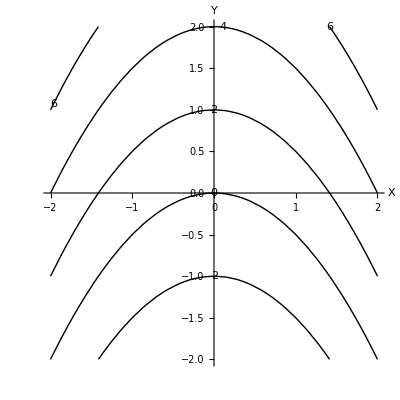

```mathematica
ContourPlot[x^2+2y,{x,-2,2},{y,-2,2}]
```

#### Parametric Plots

```mathematica
ParametricPlot3D[{u,v,u^2+2v},{u,-2,2},{v,-2,2}]
```

-Graphics3D-

#### Level Set

```mathematica
ContourPlot3D[x^2+2y-z==0,{x,-2,2},{y,-2,2},{z,-8,8}]
```

-Graphics3D-

## In-Class Group Work

These notebooks are shared with students in class (or workshop) in real time.

Come with a corresponding worksheet.

Have to do with real data.

Introduces students to new topics: partial derivatives, double integrals, scalar surface integrals, flux integrals, etc.

### Double Integrals

Measuring volume of snow in Massachusetts

Counting trees from satellite imaging.

## In-Class Demo

These notebooks are used by the instructors in class.

### Gradient Descent

Gradient descent is a mathematical optimization technique commonly used in machine learning and artificial intelligence to minimize a function. Suppose we’re minimizing a given function. Here’s a brief explanation gradient descent:

1. Start at an initial point.  
2. Calculate the gradient of the function at the given point. This gradient points in the direction of the steepest ascent. 
3. Update the starting point by moving in the direction opposite to the gradient. The size of the step taken in this direction is determined by a parameter known as the “learning rate”.
4. This process is repeated iteratively, updating the point progressively. The final point is considered an approximation of the function’s minimum.

## Individual Project: Mathematical 3D Logo Modeling

One of the more important aspects of Math21a is the understanding and mastery of 3D space. Half way through the semester, we have already seen many ways to model objects in R3: graphs of functions, level sets, parametric curves and surfaces, etc. In this optional project, you’ll use Mathematica as a 3D modeling tool to design the next 3D course logo for Math21a.

### Functions

Here are some built-it Mathematica functions you should use to create the components of your design:

#### Graphs using Plot3D

```mathematica
GraphicsRow[{
Plot3D[x^2+y^2,{x,-2,2},{y,-2,2}],
Plot3D[x^2+y^2,{x,y}∈Disk[]],
Plot3D[x^2+Sin[2y],{x,-2,2},{y,-2,2}]
}]
```

-Graphics-

#### Level Sets using CountourPlot3D

```mathematica
GraphicsRow[{
(*This is a cylinder*)
ContourPlot3D[x^2+y^2==2,{x,-2,2},{y,-2,2},{z,-2,2}],

(*This is a sphere*)
ContourPlot3D[x^2+y^2+z^2==2,{x,-2,2},{y,-2,2},{z,-2,2}],

(*This is a paraboloid*)
ContourPlot3D[x^2+y==0,{x,-2,2},{y,-2,2},{z,-2,2}]
}]
```

-Graphics-

#### Parametric Curves and Surfaces using ParametricPlot3D

```mathematica
GraphicsRow[{
(*This is a parametric curve*)
ParametricPlot3D[{Cos[t],Sin[t],t/10},{t,0,4Pi}],

(*This is a parametric surface*)
ParametricPlot3D[{u /4Cos[u],u/4 Sin[u],v},{u,0,4Pi},{v,0,4}]}]
```

-Graphics-

#### Geometric Shapes using Graphics3D

```mathematica
GraphicsRow[{
(*This is a ball*)
Graphics3D[{Green, Ball[]}],

(*This is a cylinder*)
Graphics3D[{Blue, Cylinder[]}],

(*This is a polygon*)
Graphics3D[{Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}]}],

(*This is a Cuboid*)
Graphics3D[{Red,Cuboid[{-2,-2,-2},{2,2,-1}]}]
}]
```

-Graphics-

```mathematica
Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],,Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}]
```

### Styling Options and Tricks

For visualization purposes, it is sometimes useful to modify the default output of the graphics.

#### Thickening

```mathematica
GraphicsRow[{
(*This is a helix*)
ParametricPlot3D[{Cos[t],Sin[t],t/10},{t,0,4Pi}],

(*This is a thicc helix*)
ParametricPlot3D[{Cos[t],Sin[t],t/10},{t,0,4Pi},PlotStyle->{Tube[0.03]}],

(*This is a thicker helix*)
ParametricPlot3D[{Cos[t],Sin[t],t/10},{t,0,4Pi},PlotStyle->{Tube[0.05]}]

}]
```

-Graphics-

```mathematica
GraphicsRow[{
(*This is a plane*)
ParametricPlot3D[{u Cos[v],u Sin[v],u^2},{u,0,1},{v,0,2Pi}],

(*This is a thick paraboloid*)
ParametricPlot3D[{u Cos[v],u Sin[v],u^2},{u,0,1},{v,0,2Pi},PlotStyle->Thickness[0.1]],,

(*This is a thicker paraboloid*)
ParametricPlot3D[{u Cos[v],u Sin[v],u^2},{u,0,1},{v,0,2Pi},PlotStyle->Thickness[0.2]],

}]
```

-Graphics-

#### Mesh and Axes

```mathematica
GraphicsRow[{
(*This is a cylinder*)
ContourPlot3D[x^2+y^2==2,{x,-2,2},{y,-2,2},{z,-2,2}],

(*This is a cylinder without mesh or axes*)
ContourPlot3D[x^2+y^2==2,{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None,Axes->False,Boxed->False]
}]
```

-Graphics-

#### Coloring

```mathematica
GraphicsRow[{
(*This is a caramel rolled iceream*)
ParametricPlot3D[{u /4Cos[u],u/4 Sin[u],v},{u,0,4Pi},{v,0,4}],

(*This is a chocolate rolled iceream*)
ParametricPlot3D[{u /4Cos[u],u/4 Sin[u],v},{u,0,4Pi},{v,0,4},PlotStyle->Brown],

(*This is a pistacchio rolled iceream*)
ParametricPlot3D[{u /4Cos[u],u/4 Sin[u],v},{u,0,4Pi},{v,0,4},PlotStyle->Green]
}]
```

-Graphics-

#### Moving Objects

To move an object in 3D, you may add a vector (a,b,c) to any given parametrization.

```mathematica
GraphicsRow[{
(*This is a sphere centered at (0,0,0)*)
ParametricPlot3D[{Sin[v]Cos[u],Sin[v] Sin[u],Cos[v]},{u,0,2Pi},{v,0,Pi},AxesOrigin->{0,0,0},Boxed->False],

(*This is a sphere centered at (1,0,0)*)
ParametricPlot3D[{1+Sin[v]Cos[u],Sin[v] Sin[u],Cos[v]},{u,0,2Pi},{v,0,Pi},AxesOrigin->{0,0,0},Boxed->False],

(*This is a sphere centered at (1,1,1)*)
ParametricPlot3D[{1+Sin[v]Cos[u],1+Sin[v] Sin[u],1+Cos[v]},{u,0,2Pi},{v,0,Pi},AxesOrigin->{0,0,0},Boxed->False]
}]
```

-Graphics-

### Course Logo Spring 2024

First, let’s start with the model description. The current course logo is made of the following pieces.

Two quarters of an ellipse.

Five fixed-θ elliptical longitude curves.

A spiral that matches the curvature of the ellipse.

An inner cylinder

#### Making the outer elliptical shell

Here is how to generate each piece separately in Mathematica. We use variables p1, p2, ... to represent each piece. To create two quarters of an ellipse, we can use a spherical parametrization and choose as parameter domain 0 ≤ϕ≤π and 0 ≤θ≤π/2 for the first quadrant, and 0 ≤ϕ≤π and π ≤θ≤3π/2 for the second. Note that in the formulas below we use υ=ϕ and ⋁=θ instead.

```mathematica
p1=ParametricPlot3D[{2Sin[v]2Cos[u],2Sin[v] 2Sin[u],2Cos[v]},{u,0,Pi/2},{v,0,Pi},PlotStyle->{Thickness[0.2]},ColorFunction->Function[{x,y,z,u,v},ColorData["FuchsiaTones"][y]],PlotPoints->25]
p2=ParametricPlot3D[{2Sin[v]2Cos[u],2Sin[v] 2Sin[u],2Cos[v]},{u,Pi,3Pi/2},{v,0,Pi},PlotStyle->{Thickness[0.2]},ColorFunction->Function[{x,y,z,u,v},ColorData["FuchsiaTones"][y]],PlotPoints->25]
```

-Graphics3D-

-Graphics3D-

Instead of creating each fixed curve separately, we may use Table[]. This will create the fixed-v curves for the values ⋁=π, 5π/4, 6π/4, 7π/4 and 2π.

```mathematica
p3=Table[
ParametricPlot3D[{2Sin[u]2Cos[v],2Sin[u]2Sin[v],2Cos[u]},{u,0, Pi},PlotStyle->{Tube[0.2]},ColorFunction->Function[{x,y,z,u,v},ColorData["FuchsiaTones"][y]]],
{v,0,Pi/2,Pi/8}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

#### Adding the Spiral and Cylinder

```mathematica
p4=ParametricPlot3D[{u/Pi Cos[v]Sin[u],u/Pi Cos[v]Cos[u],2Sin[v]}, {u,0,4Pi+0.3}, {v,-0.5,0.5},PlotStyle->{Thickness[0.2]},ColorFunction->Function[{x,y,z,u,v},ColorData["SunsetColors"][y]]]
p5=ParametricPlot3D[{0.2Cos[u],0.2Sin[u],v},{v,-2,2},{u,0,2Pi},PlotStyle->{Thickness[0.2]},ColorFunction->Function[{x,y,z,u,v},ColorData["SunsetColors"][y]]]
```

-Graphics3D-

-Graphics3D-

Here is our new model:

```mathematica
model=Show[p1,p2,p3,p4,p5,PlotRange->All]
```

-Graphics3D-

### 3D Printing

```mathematica
Printout3D[model,"IMaterialise"]
```

### Your code goes here!

## Challenges & Future Goals

Depending on course demands, students may need significant help

Students struggle with Notebook management, syntax, etc.

Need to train course staff to use Mathematica

Unsure best way to submit Mathematica homework and/or grade Notebooks

Implement more dataset-based activities (me)

Find a better file management system (me)

## Thanks for listening!

More examples?

## Projects from other classes

Mathematical Elements of Machine Learning

## In-class activity: Linear Algebra and Image Processing

### Basics of Image Processing

An image is, essentially, a matrix of pixels. In a grayscale image, the color is indicated by a number between 0 and 1. Values closer to 0 represent darker tones, whereas values close to 1 are lighter. It is worth noting that in other programing languages, sometimes an integer between 0 and 255 is used instead. Here is an example of a 3x3 image.

```mathematica
Image[({{0.1, 0.2, 0.3}, {0.4, 0.5, 0.6}, {0.7, 0.7, 0.9}})]
```

-Graphics-

To represent colored pictures, we need a little more information. The RGB system defines each color as a combination of “Red”, “Green” and “Blue”.  Each pixel will thus have three values, defining the amount of colors red, green and blue in it. This is an example of an image of 2x3 = 6 pixels.

```mathematica
Image[({{({{0}, {0.6}, {0}}), ({{0.4}, {0.1}, {0.8}}), ({{0.7}, {0.9}, {0.7}})}, {({{1}, {0}, {0.9}}), ({{0.6}, {0.6}, {1}}), ({{1}, {0.8}, {0.3}})}})]
```

-Graphics-

In Mathematica, there are two basic commands to translate from an image and its corresponding matrix: Image[] and ImageData[]. Let’s start by loading a close-up image of a girl using Import[]:

```mathematica
infant=Import["ExampleData/girlcloseup.jpg"]
```

-Graphics-

To see the underlying matrix, we can call ImageData[]. Of course, since this images has many pixels we are gonna get a massive matrix! To see the resolution of an image, we can call the function Dimensions[].

```mathematica
Dimensions[infantmatrix]
```

{}

The cell below shows that the image resolution is 580x580 (the last 3 represent the three RGB colors). Hence this image has 580x580 = 336400 pixels! Thankfully, Mathematica knows not to display large outputs, and will just output a sample of these pixels.

```mathematica
infantmatrix=ImageData[infant]
```

{{{1.,0.607843,0.721569},578,{0.870588,0.811765,0.658824}},578,{{1},578,{1}}}
 |  |  |  |

### Pixelwise Linear Transformations

To apply linear transformations to our pixels, we’ll first define two auxiliary functions. One for linear transformations and one for affine transformations.

```mathematica
ApplyLinearFilter[im_,mm_]:=
Image[Map[mm.#&,ImageData[im],{2}]]

ApplyAffineFilter[im_,mm_,bb_]:=
Image[Map[(mm.#+bb)&,ImageData[im],{2}]]
```

The matrix below, corresponds to the commonly used sepia filter.

```mathematica
sepia={{.393,.796,.189},{.349,.686,.168},{.272,.534,.131}};
MatrixForm[sepia]
```

(0.393 | 0.796 | 0.189
0.349 | 0.686 | 0.168
0.272 | 0.534 | 0.131)

Mathematically, each pixel (r
g
b) gets multiplied by (0.393 | 0.796 | 0.189
0.349 | 0.686 | 0.168
0.272 | 0.534 | 0.131) to produce a filter with a different color scheme, which we identify as sepia. A similar idea can be used to transform a colored image into a grayscale image. Note that each pixel in a colored image is a vector of three components (r
g
b), while in a grayscale is just a number. A transformation that takes as input a vector of three components and outputs a number if a 1x3 matrix. In this case we’ll consider (0.3 | 0.59 | 0.11).

```mathematica
grayscale1={{0.3,0.59,0.11}};
MatrixForm[grayscale1]
```

(0.3 | 0.59 | 0.11)

```mathematica
infant=Import["ExampleData/girlcloseup.jpg"];
GraphicsRow[{infant,ApplyLinearFilter[infant,sepia],ApplyLinearFilter[infant,grayscale1],ApplyLinearFilter[infant,grayscale1]}]
```

-Graphics-

```mathematica
colorswap={{0,1,0},{1,0,0},{0,0,1}};
redonly={{1,0,0},{0,0,0},{0,0,0}};
redden={{1.3,0,0},{0,1,0},{0,0,1}};
bluen={{1,0,0},{0,1,0},{0,0,1.3}};
```

```mathematica
GraphicsRow[{ApplyLinearFilter[infant,colorswap],ApplyLinearFilter[infant,redonly],ApplyLinearFilter[infant,redden],ApplyLinearFilter[infant,bluen]}]
```

-Graphics-

We haven’t talked about affine linear transformations in class, but as an example, the following transformation makes the negative of an image:

```mathematica
imageneg={{-1,0,0},{0,-1,0},{0,0,-1}};
white={1,1,1};
negativeinfant=ApplyAffineFilter[infant,imageneg,white]
```

-Graphics-

Some pixelwise transformations can be inverted. For example, the negative of a negative image should result in the original one:

```mathematica
ApplyAffineFilter[negativeinfant,imageneg,white]
```

-Graphics-

We can also invert the sepia filter by using Inverse[]

```mathematica
sepiainfant=ApplyLinearFilter[infant,sepia]
inversesepia=Inverse[sepia]
ApplyLinearFilter[sepiainfant,inversesepia]
```

-Graphics-

{{-308.,6700.,-8148.},{46.,-150.,126.},{452.,-13300.,16412.}}

-Graphics-

### Filters using Convolutions

Mathematica has a built-in function ImageConvolve[] for applying convolutions to images.

```mathematica
?ImageConvolve
```

Vertical and horizontal edge-detection filters.

```mathematica
GraphicsRow[{ImageConvolve[infant,({{-1, 0, 1}, {-2, 0, 2}, {-1, 0, 1}})],ImageConvolve[infant,({{-1, -2, -1}, {0, 0, 0}, {1, 2, 1}})]}]
```

-Graphics-

Blur filter.

```mathematica
ImageConvolve[infant,({{1, 1, 1}, {1, 1, 1}, {1, 1, 1}})/9]
```

-Graphics-

### Exercise 1

The following images have been edited using different filters. By applying some transformations, try to uncover the original image! In one of the examples, the transformation are not invertible (can’t be undone). To find the inverse of a matrix, you can use the command Inverse[].

```mathematica
hiddenpeppers=-Graphics-
```

-Graphics-

```mathematica
(*Try here to recover the peppers*)
```

```mathematica
hiddenrose=-Graphics-
```

-Graphics-

```mathematica
ApplyLinearFilter[hiddenrose,Inverse[sepia]]
```

-Graphics-

```mathematica
(*Try here to recover the rose*)
```

```mathematica
hiddenmandril=-Graphics-
```

-Graphics-

```mathematica
(*Try here to recover the mandril*)
```

Once you are happy with  your result, compare it to the actual original images by running the code below:

```mathematica
Import["ExampleData/rose.gif"]
ExampleData[{"TestImage","Peppers"}]
ExampleData[{"TestImage","Mandrill"}]
```

-Graphics-

-Graphics-

-Graphics-

### Exercise 2

Although at first it may seem counterintuitive, a grayscale image can be represented by an RGB matrix. In fact, the same proportion of green, red and blue will always produce a color in the gray scale. Here are some examples:

```mathematica
Image[{{{0.1,0.1,0.1}}}]
Image[{{{0.9,0.9,0.9}}}]
Image[{{{0.4,0.4,0.4}}}]
```

-Graphics-

-Graphics-

-Graphics-

If there is the slightest higher proportion of one of the colors, we can clearly see it. Here, although light, we can clearly see a green square. This is because there is slightly more green 0.5, than red or blue, both 0.4.

```mathematica
Image[{{{0.4,0.5,0.4}}}]
```

-Graphics-

Can you come up with a 3x3 matrix, that converts an RGB image, to a grayscale RGB image by pixelwise multiplication?

## Group Project: Designing a Neural Network

### Net Encoders/Decoders

```mathematica
trainingData=ResourceData["MNIST","TrainingData"];
testData=ResourceData["MNIST","TestData"];
```

### Net Encoders/Decoders

Once we have the data, we must set up a way to encode the data (our input will be lots of small images) and to specify the output that we expect . In this case : 
	• The input will be grayscale images of size 28*28
	• The output shall be a single digit number ranging from 0 to 9.
	
To do this, we use the commands NetEncoder and NetDecoder

```mathematica
mnistEncoder=NetEncoder[{"Image",{28,28},"ColorSpace"->"Grayscale"}];

mnistDecoder=NetDecoder[{"Class",Range[0,9]}];
```

### Designing a Network Structure

The command NetChain specifies a neural network by concatenating the provided list of layers. Implementing LeNet is thus done as follows.

```mathematica
uninitializedNet=NetChain[{
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
ConvolutionLayer[50,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
FlattenLayer[],
LinearLayer[500],
ElementwiseLayer[Ramp],
LinearLayer[10],
SoftmaxLayer[]
},
"Input"->mnistEncoder,
"Output"->mnistDecoder];
```

The previous code only creates the neural network. The learnable parameters do not have any initial values yet. We must explicitly initialize them via:

```mathematica
initializedNet=NetInitialize[uninitializedNet];
```

Now the network has been initialized, but since we haven’t trained it yet, we don’t expect it to yield any valuable results:

```mathematica
initializedNet[-Graphics-]
```

1

#### Understanding Layers

```mathematica
LinearLayer[100,"Input"->{200}]
```

LinearLayer[<>]

### Training the Neural Network

In order to train our network we must provide a way to evaluate it. So far, our network accepts a single input (an image) and returns a single number (the estimated digit). If we want to train our network, we must be able to feed it the input image together with its known label. To this end we must convert it to a graph and add a cross entropy layer as loss estimate.

```mathematica
trainingNet=NetGraph[<|"MyNet"->initializedNet,"loss"->CrossEntropyLossLayer["Index"]|>,{NetPort["Input"]->"MyNet"->NetPort["loss","Input"],NetPort["Target"]->NetPort["loss","Target"]}]
```

NetGraph[<>]

In the code above, the first part specifies the available networks and layers. The second part specifies how everything is connected. Besides our network (now named “MyNet”) we have added a layer “loss”, which is given by a cross entropy layer. Input data goes to the “Input” port of our network, flows through “MyNet” and into the “Input” port of the “loss” layer. The data labels go to the “Target” port of our network and flow directly to the “Target” port of our “loss” layer.

In order to train our network we must specify some training data and some validation data.

```mathematica
trainAssoc=<|"Input"->Keys[trainingData],"Target"->Values[trainingData]+1|>;
testAssoc=<|"Input"->Keys[testData],"Target"->Values[testData]+1|>;
results=NetTrain[trainingNet,trainAssoc,All,ValidationSet->testAssoc,MaxTrainingRounds->5];
```

The +1 is necessary because our labels are digits going from 0 to 9, our loss function however works with indices of a list of 10 probabilities. Since array indices are 1 based in Mathematica, we must add 1 to each value. Training is now straightforward.

```mathematica
trainedNet=NetExtract[results["TrainedNet"],"MyNet"];
trainedNet=NetReplacePart[trainedNet,{"Input"->mnistEncoder,"Output"->mnistDecoder}];
```

As a final step we remove the cross entropy layer and reattach the original input/output encoders and decoders.

```mathematica
trainedNet[-Graphics-]
```

0